```mathematica
(* 
        CALCULATE EFFECTIVE HAMILTOIAN IN *ONE* FUNCTION
*)
```

```mathematica
Quit[]
```

```mathematica
(* INITIALIZATION *)
```

```mathematica
(* INPUT 1 *)

(* Generic Hamiltonian weak driving
H[t_]=H1/4 (Cos[phi]sx+sx Cos[2 t ww+phi]+Sin[phi]sy-sy Sin[2 t ww+phi])+(Delta/2)sz/.phi->0/.Delta->0;
*)
(* Generic Hamiltonian (strong driving) *)
H[t_]:=ΔSym/2(sx Cos[2 α]-sy Sin[2 α])/.α:>H0Sym/4 t+H1Sym/2 Sin[ww t]/.ΔSym:>ΔV;

(* set maximum order of 1/ww, and set up list of coefficients (for sTrim),  in case of taylor == True 
the highest "reasonable" max is 5 *)
max=0;

(* coeffs1 = time-dependent coefficients of original Hamiltonian [no derivatives] *)
coeffs1={{H0Sym,1},{H1Sym,1},{ΔSym,1}};

(*offResonant = True or False*)
offResonant=False;

(*taylor Expansion = True or False*)
taylor=False;

(* how much output should be written *)
verbose=False;
verboseLight=False;
(*verbose=True;
verboseLight=True;*)
(*t0=0;*)


myDir=NotebookDirectory[];
nb1=NotebookOpen[myDir <> "/scripts/Magnus_script_precalculated.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
t0=0;
```

```mathematica
NotebookSave[nb1];
NotebookClose[nb1];

(* contains NCAlgebra initialization and MagnusM and MAgnusM2 *)
nb2=NotebookOpen[myDir <> "/scripts/Magnus_script1.nb"];
SelectionMove[nb2,All,Notebook];
SelectionEvaluate[nb2];
```

```mathematica
(* INPUT *)
(* coefficients="simple" 
in case there are at most two coefficients, which need to be called H1 and H2 *)
coefficients="simple";
coefficients="NotSoSimple";
If[coefficients=="simple",
updateCoeffsSimple,
(*otherwise determine the coefficients laboriously*)
updateCoeffs;
];
myCList
```

{{{H0Sym},1},{{H1Sym},1},{{ΔSym},1}}

```mathematica
NotebookSave[nb2];
NotebookClose[nb2];
```

```mathematica
(*$RecursionLimit=5000*)
```

```mathematica
tc
```

(2 π)/ww

```mathematica
(* for final integral, use FastIntegral *)
(*experimental notebook.*)
(**tryout, we have changed //S -> Expand**)
AbsoluteTiming[M[H[t]/.H0Sym->2ww,max]]
```

should be False:  taylor = False

Special step:  sTrim has been temporarily modified

My Hamiltonian = 1/2 sx ΔV Cos[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]-1/2 sy ΔV Sin[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]

Begin calculating ΩΩ_k/Omega_k of order k = 1, at date and time {2018,8,30,22,46,16.497055}

Now:  final integral

{521.1018053,(ⅈ ww ∫_t0^(t0+(2 π)/ww) -1/2 ⅈ ΔV (sx Cos[tt ww+H1Sym Sin[tt ww]]-sy Sin[tt ww+H1Sym Sin[tt ww]])ⅆtt)/(2 π)}

```mathematica
AbsoluteTiming[M[H[t]/.H0Sym->2ww,max]]
```

INPUT: HH = 1/2 ΔV (sx Cos[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]-sy Sin[2 ((t ww)/2+1/2 H1Sym Sin[t ww])])

HH = 1/2 sx ΔV Cos[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]-1/2 sy ΔV Sin[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]

HH = 1/2 sx ΔV Cos[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]-1/2 sy ΔV Sin[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]

should be False:  taylor = False

Special step:  sTrim has been temporarily modified

My Hamiltonian = 1/2 sx ΔV Cos[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]-1/2 sy ΔV Sin[2 ((t ww)/2+1/2 H1Sym Sin[t ww])]

Begin calculating ΩΩ_k/Omega_k of order k = 1, at date and time {2018,8,30,22,38,55.3108207}

Now:  final integral

{107.460146,-1/2 sx ΔV BesselJ[1,H1Sym]}

```mathematica
Print["Result"]
```

Result

```mathematica
(*Integrals that yield Bessel functions*)
```

```mathematica
myInt:=ⅈ ww ∫_0^((2 π)/ww) -1/2 ⅈ ΔV (sx Cos[(H0Sym tt)/2+H1Sym Sin[tt ww]]-sy Sin[(H0Sym tt)/2+H1Sym Sin[tt ww]])ⅆtt
myInt15:=ⅈ ww ∫_0^((2 π)/ww) -1/2 ⅈ ΔV (sx Cos[2ww tt+H1Sym/2 Sin[tt ww]]-sy Sin[2ww tt+H1Sym/2 Sin[tt ww]])ⅆtt
myInt2:=ⅈ ww ∫_0^((2 π)/ww) -1/2 ⅈ ΔV (sx Cos[ww tt+H1Sym Sin[tt ww]]-sy Sin[ww tt+H1Sym Sin[tt ww]])ⅆtt
```

```mathematica
Cos[a+b]//TrigExpand
```

Cos[a] Cos[b]-Sin[a] Sin[b]

```mathematica
myInt2
```

-π sx ΔV BesselJ[1,H1Sym]

```mathematica
myInt15
```

ConditionalExpression[π sx ΔV BesselJ[2,Abs[H1Sym]/2],H1Sym∈Reals]

```mathematica
?BesselJ
```

BesselJ[n,z] gives the Bessel function of the first kind J_n(z).

```mathematica
Integrate[BesselJ[0,z],z]
Integrate[BesselJ[0,z],{z,0,2Pi}]
```

z HypergeometricPFQ[{1/2},{1,3/2},-z^2/4]

2 π HypergeometricPFQ[{1/2},{1,3/2},-π^2]

```mathematica
?HypergeometricPFQ
```

HypergeometricPFQ[{a_1,…,a_p},{b_1,…,b_q},z] is the generalized hypergeometric function _p F_q(a;b;z).

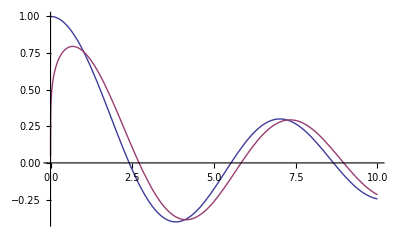

```mathematica
Plot[{BesselJ[0,z],BesselJ[.2,z]},{z,0,10}]
```

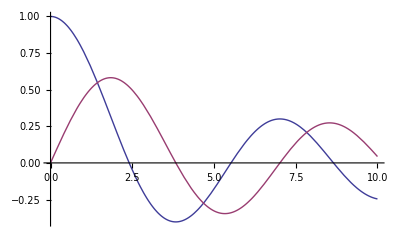

```mathematica
Plot[{BesselJ[0,z],BesselJ[1,z]},{z,0,10}]
```

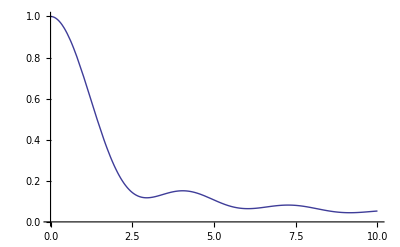

```mathematica
Plot[HypergeometricPFQ[{1/2},{1,3/2},-z^2],{z,0,10}]
```

```mathematica
D[BesselJ[0,z],z]
D[BesselJ[1,z],z]
D[BesselJ[2,z],z]
D[BesselJ[n,z],z]
```

-BesselJ[1,z]

1/2 (BesselJ[0,z]-BesselJ[2,z])

1/2 (BesselJ[1,z]-BesselJ[3,z])

1/2 (BesselJ[-1+n,z]-BesselJ[1+n,z])

```mathematica
-1/(14495514624 ww^8)H1 (21745 H1^8 sx+7496 H1^7 sz ww+392832 H1^6 sx ww^2+1124352 H1^5 sz ww^3+5308416 H1^4 sx ww^4+28311552 H1^3 sz ww^5+56623104 H1^2 sx ww^6+452984832 H1 sz ww^7-3623878656 sx ww^8)//Expand
```

(H1 sx)/4-(21745 H1^9 sx)/(14495514624 ww^8)-(937 H1^8 sz)/(1811939328 ww^7)-(341 H1^7 sx)/(12582912 ww^6)-(61 H1^6 sz)/(786432 ww^5)-(3 H1^5 sx)/(8192 ww^4)-(H1^4 sz)/(512 ww^3)-(H1^3 sx)/(256 ww^2)-(H1^2 sz)/(32 ww)

```mathematica
{1,8,64,128,2048,196608,3145728,452984832,3623878656}
```

{4,32,256,512,8192,786432,12582912,1811939328,14495514624}

```mathematica
NotebookSave[]
```

```mathematica
Date[][[1;;5]]
```

{2018,7,15,18,55}

```mathematica
NotebookSave[]
```

Result up to order 1/ww^7

{222.286,1/(1811939328 ww^7)H1 (-5076 H1^7 sz-58752 H1^6 sx ww-20736 H1^5 sz ww^2-995328 H1^4 sx ww^3+884736 H1^3 sz ww^4-14155776 H1^2 sx ww^5+56623104 H1 sz ww^6+452984832 sx ww^7+216 H1 (47 H1^6 sz+56 H1^5 sx ww+192 H1^4 sz ww^2+2560 H1^3 sx ww^3-8192 H1^2 sz ww^4+65536 H1 sx ww^5-524288 sz ww^6) Cos[2 t0 ww]-48 H1^2 (91 H1^5 sz-84 H1^4 sx ww+2880 H1^3 sz ww^2+2304 H1^2 sx ww^3+55296 H1 sz ww^4+147456 sx ww^5) Cos[4 t0 ww]-1540 H1^7 sz Cos[6 t0 ww]-5760 H1^6 sx ww Cos[6 t0 ww]-23040 H1^5 sz ww^2 Cos[6 t0 ww]-110592 H1^4 sx ww^3 Cos[6 t0 ww]-105 H1^7 sz Cos[8 t0 ww]-720 H1^6 sx ww Cos[8 t0 ww]+12096 H1^6 sy ww Sin[2 t0 ww]+552960 H1^4 sy ww^3 Sin[2 t0 ww]+14155776 H1^2 sy ww^5 Sin[2 t0 ww]+16128 H1^6 sy ww Sin[4 t0 ww]+442368 H1^4 sy ww^3 Sin[4 t0 ww]+7077888 H1^2 sy ww^5 Sin[4 t0 ww]+7680 H1^6 sy ww Sin[6 t0 ww]+110592 H1^4 sy ww^3 Sin[6 t0 ww]+720 H1^6 sy ww Sin[8 t0 ww])}